```mathematica
ClearAll["Global`*"]
```

```mathematica
toCPP[u_]:=StringReplace[ToLowerCase@ToString@CForm@#,{"x"->"p[0]","y"->"p[1]","pi"-> "PI","3.141592653589793"->"PI"," 1.*"->""," 1*"->"","*1. "->"","*1 "->"","power"->"pow"}]&/@u
```

```mathematica
<<Notation`
Symbolize[ℛℯ^_]
Symbolize[n̄]
Symbolize[Subscript[p, _]]
```

## Model Domain

### Analytic Region

```mathematica
Ω=Rectangle[{0,0},{1,1}];
```

```mathematica
RegionPlot[Ω,AspectRatio->Automatic]
```

### Triangulation

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../../../Tools/Mathematica/triangulation.nb"]
```

```mathematica
𝒯=create𝒯fromRegion[Ω,.1,.3];
```

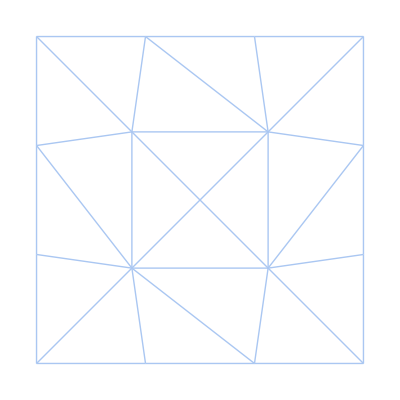

```mathematica
highlight[𝒯,{},0]
```

```mathematica
SetDirectory@NotebookDirectory[];
export@𝒯
```

mesh.ntn

## PDE

### Input Data

α u + (w . ∇)u - ℛℯ^-1 Δ u + ∇p = f,
∇ . u = g,

u|_Γ_in = u_in, u|_Γ_0 = 0,
(ℛℯ^-1(∂u)/(∂n̂) - p n̂)|_Γ_out = h

Velocity field:

```mathematica
u[x_,y_]:={-4(2y−1)(1−x)x,4(2x−1)(1−y)y}
toCPP@u[x,y]
```

Pressure distribution:

```mathematica
p[x_,y_]:=4y(1-x)(1-y)(*Cos[π(x+y)]+1*)
pMean=0(*∫_({x,y}∈Ω) p[x,y]*);
Subscript[p, 0][x_,y_]:=p[x,y]-pMean
Plot3D[Subscript[p, 0][x,y],{x,y}∈Ω,Mesh->None]
toCPP@Subscript[p, 0][x,y]
```

Other parameters:

```mathematica
α=1;
```

```mathematica
w[x_,y_]:={x,-y}
VectorPlot[w[x,y],{x,y}∈Ω]
toCPP@w[x,y]
```

```mathematica
(*ℛℯ^-1=1;*)
```

```mathematica
n̂[x,y]:={1,0}
```

### Computed Data

Force term:

```mathematica
f[x_,y_]=FullSimplify[α u[x,y]+(w[x,y].{D[#, x],D[#, y]})&@u[x,y]-ℛℯ^-1 Laplacian[u[x,y],{x,y}]+Grad[Subscript[p, 0][x,y],{x,y}]];
toCPP@f[x,y]
```

“Continuity” term:

```mathematica
g[x_,y_]=FullSimplify@Div[u[x,y],{x,y}];
toCPP@g[x,y]
```

Neumann value:

```mathematica
MatrixForm@Grad[u[x,y],{x,y}]
```

```mathematica
h[x_,y_]=FullSimplify[(ℛℯ^-1 Grad[u[x,y],{x,y}]-Subscript[p, 0][x,y]IdentityMatrix@2).n̂[x,y]];
toCPP@h[x,y]
```

### Plot

```mathematica
velocityPlot=VectorDensityPlot[u[x,y],{x,y}∈Ω,
ColorFunction->"DeepSeaColors",
PlotLegends->Automatic,
AspectRatio->Automatic,
ImageSize->Medium
];
pressurePlot=StreamDensityPlot[{u[x,y],Subscript[p, 0][x,y]},{x,y}∈Ω,
StreamStyle->{White},
ColorFunction->"DarkRainbow",
PlotLegends->Automatic,
AspectRatio->Automatic,
ImageSize->Medium
];
```

```mathematica
Grid[{{velocityPlot,pressurePlot}}]
```